```mathematica
LaunchKernels[];
```

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
ParallelNeeds["NumericalDifferentialEquationAnalysis`"]
```

### Gauss-Legendre quadrature

GaussianQuadratureWeights[n,a,b] gives weights and abscissae over [a,b] ... note also, symmetric, therefore ∫_(-1/2)^(1/2) =2∫_0^(1/2)

```mathematica
n=10;
a=0;
b=1/2;
gq=GaussianQuadratureWeights[n,a,b];
zi=NSolve[LegendreP[n,x]==0,x][[All,1,-1]];
wi=2/((1-zi^2) (D[LegendreP[10,x],x] /. x->zi)^2);
zi=(b-a)/2 zi + (a+b)/2;
wi*=(b-a)/2;
{gq // MatrixForm,Partition[Riffle[zi,wi],2] // MatrixForm}
```

{(0.00652337 | 0.0166678
0.0337342 | 0.0373628
0.0801476 | 0.0547716
0.141651 | 0.0673167
0.212781 | 0.0738811
0.287219 | 0.0738811
0.358349 | 0.0673167
0.419852 | 0.0547716
0.466266 | 0.0373628
0.493477 | 0.0166678),(0.00652337 | 0.0166678
0.0337342 | 0.0373628
0.0801476 | 0.0547716
0.141651 | 0.0673167
0.212781 | 0.0738811
0.287219 | 0.0738811
0.358349 | 0.0673167
0.419852 | 0.0547716
0.466266 | 0.0373628
0.493477 | 0.0166678)}

### Preliminaries

```mathematica
L=2;
β = 0.5;
g[Δ_,k_]:=(Sinc[ π (k+Δ)] Cos[β π (k+Δ)])/(1-(2 β (k+Δ))^2);
M=20;
Tm=Table[(2 m + 1)!,{m,0,M-1}]*CoefficientList[Normal[Series[Tan[x],{x,0,2 M - 1}]],x][[Range[2,2 M,2]]];
```

```mathematica
gnew[α1_,Δ1_,α2_,Δ2_,k_]:=α1^2*g[Δ1,k]+α2^2*g[Δ2,k];
GC[L_,σΔ_,SNRdB_,M_,α1i_,Δ1i_,α2i_,Δ2i_]:=Module[{scale,σv,α,σX,n,i,gk,k,κ,m},
scale=gnew[α1i,Δ1i,α2i,Δ2i,0];
σv=(α1i+α2i)√((L^2-1)/(3*Log[2,L]*10^(SNRdB/10)));
α=Table[0,{M}];
σX=0;
gk=Join[Table[gnew[α1i,Δ1i,α2i,Δ2i,k],{k,-40,-1}],Table[gnew[α1i,Δ1i,α2i,Δ2i,k],{k,1,40}]];
κ=Table[(-1)^(m+1) Tm[[m]] (L^(2 m) - 1)/(2^(2 m) - 1) Total[gk^(2 m)],{m,1,M}];
For[m=2,m≤M,
α[[m]]=κ[[m]] + ∑_(i=2)^(m-2) Binomial[2 m - 1,2 i] κ[[m-i]] α[[i]];
m++];
σX=√(κ[[1]] + σv^2);
{scale,σX,α}];
```

```mathematica
GetGCPDF[L_,σΔ_,SNRdB_,M_,α1_,Δ1_,α2_,Δ2_,y_]:=Module[{gq,Δi,wi,GCparams,scale,σX,α,i,m,roots},
GCparams=GC[L,σΔ,SNRdB,M,α1,Δ1,α2,Δ2];
scale=GCparams[[1]];
σX=GCparams[[2]];
α=GCparams[[3]];
1/(√(2 π) σX) Exp[-(y - scale)^2/(2 σX^2)] (1 + ∑_(m=2)^M α[[m]]/((2 m)! σX^(2 m)) 2^-m HermiteH[2 m,(y - scale)/(√2 σX)])-1/(√(2 π) σX) Exp[-(y - 3scale)^2/(2 σX^2)] (1 + ∑_(m=2)^M α[[m]]/((2 m)! σX^(2 m)) 2^-m HermiteH[2 m,(y - 3scale)/(√2 σX)])];
```

```mathematica
PlotGC[L_,σΔ_,SNRdB_,M_,α1_,Δ1_,α2_,Δ2_,pa_,pb_,ylims_]:=Module[{gq,Δi,wi,GCparams,scale,σX,α,i,y,m,roots},
GCparams=GC[L,σΔ,SNRdB,M,α1,Δ1,α2,Δ2];
scale=GCparams[[1]];
σX=GCparams[[2]];
α=GCparams[[3]];
Plot[GetGCPDF[L,σΔ,SNRdB,M,α1,Δ1,α2,Δ2,y],{y,pa,pb},PlotRange->ylims,PlotLabel->"r1="<>ToString[α1]<>" t1="<>ToString[Δ1]<>" r2="<>ToString[α2]<>" t2="<>ToString[Δ2]]];
```

```mathematica
optboundaries[L_,σΔ_,SNRdB_,M_,α1_,Δ1_,α2_,Δ2_]:=Module[{gq,Δi,wi,GCparams,scale,σX,α,i,y,m,roots},
GCparams=GC[L,σΔ,SNRdB,M,α1,Δ1,α2,Δ2];
scale=GCparams[[1]];
σX=GCparams[[2]];
α=GCparams[[3]];
roots=FindRoot[1/(√(2 π) σX) Exp[-(y - scale)^2/(2 σX^2)] (1 + ∑_(m=2)^M α[[m]]/((2 m)! σX^(2 m)) 2^-m HermiteH[2 m,(y - scale)/(√2 σX)])-1/(√(2 π) σX) Exp[-(y - 3scale)^2/(2 σX^2)] (1 + ∑_(m=2)^M α[[m]]/((2 m)! σX^(2 m)) 2^-m HermiteH[2 m,(y - 3scale)/(√2 σX)]),{y,2(α1^2+α2^2)},PrecisionGoal->0,AccuracyGoal->4];
roots[[1,2]]];
```

```mathematica
GetBER[L_,σΔ_,SNRdB_,M_,α1_,Δ1_,α2_,Δ2_,roots_] := Module[{GCparams,scale,σX,α,BER},
GCparams=GC[L,σΔ,SNRdB,M,α1,Δ1,α2,Δ2];
scale=GCparams[[1]];
σX=GCparams[[2]];
α=GCparams[[3]];
BER=NIntegrate[1/(√(2 π) σX) Exp[-(y - scale)^2/(2 σX^2)] (1 + ∑_(m=2)^M α[[m]]/((2 m)! σX^(2 m)) 2^-m HermiteH[2 m,(y - scale)/(√2 σX)]),{y,roots,roots+5},PrecisionGoal->4]+NIntegrate[1/(√(2 π) σX) Exp[-(y - 3scale)^2/(2 σX^2)] (1 + ∑_(m=2)^M α[[m]]/((2 m)! σX^(2 m)) 2^-m HermiteH[2 m,(y - 3scale)/(√2 σX)]),{y,roots-5,roots},PrecisionGoal->4];
BER];
```

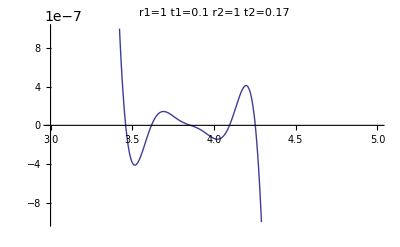

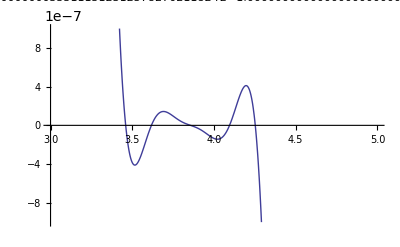

4

3.80933

```mathematica
ra=1;
rb=1;
ta=0.1;
tb=0.17;
PlotGC[L,√0.001,20,M,ra,ta,rb,tb,3,5,{-10^-6,10^-6}]
PlotGC[SetPrecision[L,40],SetPrecision[√0.001,40],SetPrecision[20,40],SetPrecision[M,40],SetPrecision[ra,40],SetPrecision[ta,40],SetPrecision[rb,40],SetPrecision[tb,40],3,5,{-10^-6,10^-6}]
2(ra^2+rb^2)
optboundaries[L,√0.001,20,M,ra,ta,rb,tb]
```

```mathematica
Manipulate[GraphicsColumn[{PlotGC[L,√0.001,20,M,r1,t1,r2,t2,3,5,All],optboundaries[L,√0.001,20,M,r1,t1,r2,t2]},Alignment->Top],{r1,0.3,3},{r2,0.3,3},{t1,0.001,0.3},{t2,0.001,0.3}]
```

```mathematica
step=0.05;
stop=0.5;
testplot=Table[optboundaries[L,√0.001,20,M,0.3,a,0.3,b],{a,0.2,stop,step},{b,0.2,stop,step}];
```

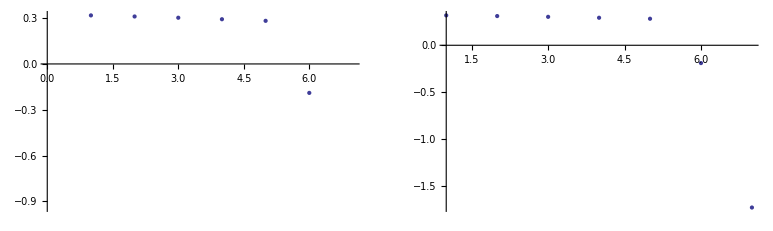

```mathematica
GraphicsRow[{ListPlot[testplot[[3]],PlotStyle->PointSize[Large]],
ListPlot[testplot[[3]],PlotStyle->PointSize[Large],PlotRange->All]}]
```

```mathematica
MatrixPlot[testplot,PlotLegends->Automatic]
```

```mathematica
ListDensityPlot[testplot,ColorFunction->"Rainbow",PlotRange->{0,2},DataRange->{{0.2,0.5},{0.2,0.5}},PlotLegends->Automatic]
```

```mathematica
σΔ=√0.001;
SNRdB=20;
```

```mathematica
Tikhonov[y_,σ_]:=Tikhonov[y,σ]=Exp[Cos[2 Pi y]/(2Pi σ)^2]/BesselI[0,1/(2 Pi σ)^2]
Rayleigh[y_]:=Rayleigh[y]=PDF[NakagamiDistribution[1,2 (Sqrt[2/Pi] )^2],y]
σΔ1=0.01;
σΔ2=0.01;
```

Average the conditional BER over the distributions (Gauss-Legendre for Tikhonov, I used a linear sampling for the Rayleigh)

```mathematica
gqtikh1=GaussianQuadratureWeights[2,0,0.3];
gqtikh2=GaussianQuadratureWeights[2,0,0.3];
iΔ1=gqtikh1[[All,1]];
wΔ1=gqtikh1[[All,2]];
sizeΔ1=Length[iΔ1];
iΔ2=gqtikh2[[All,1]];
wΔ2=gqtikh2[[All,2]];
sizeΔ2=Length[iΔ2];
ir1 = Join[Range[0.3,1,0.5],Range[1,3,2]];
wr1=Table[1/Length[ir1],{Length[ir1]}];
sizer1=Length[ir1];
ir2 =Join[Range[0.3,1,0.5],Range[1,3,2]];
wr2=Table[1/Length[ir2],{Length[ir2]}];
sizer2=Length[ir2];
iΔ1grid = Table[iΔ1[[c]],{c,sizeΔ1},{sizeΔ2},{sizer1},{sizer2}];
wΔ1grid = Table[wΔ1[[c]],{c,sizeΔ1},{sizeΔ2},{sizer1},{sizer2}];
iΔ2grid = Table[iΔ2[[c]],{sizeΔ1},{c,sizeΔ2},{sizer1},{sizer2}];
wΔ2grid = Table[wΔ2[[c]],{sizeΔ1},{c,sizeΔ2},{sizer1},{sizer2}];
ir1grid = Table[ir1[[c]],{sizeΔ1},{sizeΔ2},{c,sizer1},{sizer2}];
wr1grid = Table[wr1[[c]],{sizeΔ1},{sizeΔ2},{c,sizer1},{sizer2}];
ir2grid = Table[ir2[[c]],{sizeΔ1},{sizeΔ2},{sizer1},{c,sizer2}];
wr2grid = Table[wr2[[c]],{sizeΔ1},{sizeΔ2},{sizer1},{c,sizer2}];
iΔ1grid[[All,1,1,1]]
iΔ2grid[[1,All,1,1]]
ir1grid[[1,1,All,1]]
ir2grid[[1,1,1,All]]
AbsoluteTiming[pdflist = Table[GetGCPDF[L,σΔ,SNRdB,M,ir1grid[[a,b,c,d]],iΔ1grid[[a,b,c,d]],ir2grid[[a,b,c,d]],iΔ2grid[[a,b,c,d]],y],{a,sizeΔ1},{b,sizeΔ2},{c,sizer1},{d,sizer2}];]
AbsoluteTiming[pdfs = Total[wΔ1grid*Tikhonov[iΔ1grid,σΔ1]*wΔ2grid*Tikhonov[iΔ2grid,σΔ2]*pdflist,2];]
AbsoluteTiming[roots = Table[FindRoot[pdfs[[c,d]],{y,2(ir1grid[[a,b,c,d]]^2+ir1grid[[a,b,c,d]]^2)},PrecisionGoal->3][[1,2]],{a,sizeΔ1},{b,sizeΔ2},{c,sizer1},{d,sizer2}];]
AbsoluteTiming[unweightedBER=Table[GetBER[L,σΔ,SNRdB,M,ir1grid[[a,b,c,d]],iΔ1grid[[a,b,c,d]],ir2grid[[a,b,c,d]],iΔ2grid[[a,b,c,d]],roots[[a,b,c,d]]],{a,sizeΔ1},{b,sizeΔ2},{c,sizer1},{d,sizer2}];]
AbsoluteTiming[unweightedoldBER=Table[GetBER[L,σΔ,SNRdB,M,ir1grid[[a,b,c,d]],iΔ1grid[[a,b,c,d]],ir2grid[[a,b,c,d]],iΔ2grid[[a,b,c,d]],2(ir1grid[[a,b,c,d]]^2+ir2grid[[a,b,c,d]]^2)],{a,sizeΔ1},{b,sizeΔ2},{c,sizer1},{d,sizer2}];]
AbsoluteTiming[weightedBER = wΔ1grid*Tikhonov[iΔ1grid,σΔ1]*wΔ2grid*Tikhonov[iΔ2grid,σΔ2]* wr1grid*Rayleigh[ir1grid]* wr2grid*Rayleigh[ir2grid]*unweightedBER;]
AbsoluteTiming[weightedoldBER = wΔ1grid*Tikhonov[iΔ1grid,σΔ1]*wΔ2grid*Tikhonov[iΔ2grid,σΔ2]* wr1grid*Rayleigh[ir1grid]* wr2grid*Rayleigh[ir2grid]*unweightedoldBER;]
BER = Total[weightedBER,4]
oldBER=Total[weightedoldBER,4]
```

{0.0633975,0.236603}

{0.0633975,0.236603}

{0.3,0.8,1,3}

{0.3,0.8,1,3}

{0.6084,Null}

{0.0312,Null}

{8.5644,Null}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{72.0252,Null}

{71.8224,Null}

{0.,Null}

{0.,Null}

1.72531×10^-17

9.3156×10^-21

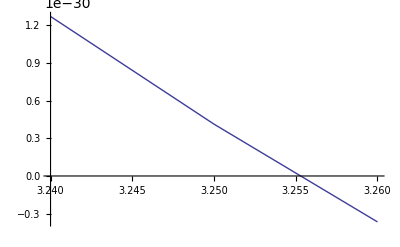

```mathematica
ListLinePlot[Table[{y,pdfs[[2,3]]},{y,3.24,3.26,0.01}]]
```

```mathematica
roots[[1,1,2,3]]
```

3.2553

```mathematica
Dimensions[Total[Table[Range[5][[c]],{c,1},{2},{3},{4}],2]]
```

{3,4}